LexicalCases Overview |

Installationpaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#580651078 | Built-in String Functionspaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#323829644
Introductionpaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#652844990 | Abstractionspaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#739144260
LexicalSummary Propertiespaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#1668282004 | Conclusionpaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#2118948183
Searching Files and Servicespaclet:FaizonZaman/LexicalCases/tutorial/LexicalCasesOverview#156924819 |

Installation

This paclet is hosted on the Wolfram Paclet Repositoryhttps://resources.wolframcloud.com/PacletRepository/. First install the paclet from the ResourceObjectpaclet:ref/ResourceObject, then load it with Needspaclet:ref/Needs.

Install the paclet and load its definitions with Needs

```mathematica
PacletInstall[ResourceObject["FaizonZaman/LexicalCases"]];
Needs["FaizonZaman`LexicalCases`"]
```

Introduction

Where StringCasespaclet:ref/StringCases aims for character patterns and TextCasespaclet:ref/TextCases for text patterns, LexicalCases aims for lexical patterns. This is accomplished by expanding the scope of StringExpression where types can be expressed anywhere within. Listed below are the pattern types one can use when searching at the lexical level.

TextTypepaclet:FaizonZaman/LexicalCases/ref/TextTypeFaizonZaman Package Symbol["type"] | Represents a TextContentTypepaclet:guide/TextContentTypes
TextTypepaclet:FaizonZaman/LexicalCases/ref/TextTypeFaizonZaman Package Symbol[t__1|…|t__i] | Represents any of the t_i
BoundTokenpaclet:FaizonZaman/LexicalCases/ref/BoundTokenFaizonZaman Package Symbol[lp] | Represents a lexical pattern bounded by WordBoundarypaclet:ref/WordBoundary
BoundTokenpaclet:FaizonZaman/LexicalCases/ref/BoundTokenFaizonZaman Package Symbol[lp__1|…|lp__i] | Represents any of the lp__i with explicit boundaries
BoundTokenpaclet:FaizonZaman/LexicalCases/ref/BoundTokenFaizonZaman Package Symbol[outer,inner] | Represents a string with inner bounded by outer
WordTokenpaclet:FaizonZaman/LexicalCases/ref/WordTokenFaizonZaman Package Symbol[n] | Represents n words separated by whitespace
WordTokenpaclet:FaizonZaman/LexicalCases/ref/WordTokenFaizonZaman Package Symbol[n,m] | Represents n to m words seperated by whitespace
WordTokenpaclet:FaizonZaman/LexicalCases/ref/WordTokenFaizonZaman Package Symbol[n,"KeepContractions"] | Considers contractions as a single word
WordTokenpaclet:FaizonZaman/LexicalCases/ref/WordTokenFaizonZaman Package Symbol[n,m,"KeepContractions"] | Represents n to m words with contractions as single words
OptionalTokenpaclet:FaizonZaman/LexicalCases/ref/OptionalTokenFaizonZaman Package Symbol[lp] | Represents an optional lexical pattern

Additional pattern constructs made available by the LexicalCases paclet.

Here we can search the Origin Of Species for adverb~adjective patterns ending with "specie" or "species". Note the whitespace string between TextTypepaclet:FaizonZaman/LexicalCases/ref/TextTypeFaizonZaman Package Symbol["Adjective"] and BoundTokenpaclet:FaizonZaman/LexicalCases/ref/BoundTokenFaizonZaman Package Symbol. Whitespace is given "for free" between some tokens like TextTypepaclet:FaizonZaman/LexicalCases/ref/TextTypeFaizonZaman Package Symbol. LexicalCasespaclet:FaizonZaman/LexicalCases/ref/LexicalCasesFaizonZaman Package Symbol returns a LexicalSummarypaclet:FaizonZaman/LexicalCases/ref/LexicalSummaryFaizonZaman Package Symbol object with several properties.

Search the origin of species for a lexical pattern

```mathematica
oosp = ExampleData[{"Text","OriginOfSpecies"}];
```

```mathematica
ols=LexicalCases[oosp, TextType["Adverb"]~~TextType["Adjective"]~~" "~~BoundToken["specie"|"species"]]
```

LexicalSummary[…]

LexicalSummary Properties

LexicalSummary properties vary in output from data to metadata. One can access various forms of the results, including the data, and their visualization.

"Data" | Returns a list of Associations which contain the match and related metadata like string position
"Dataset" | Returns "Data" as a Datasetpaclet:ref/Dataset
"Counts" | Returns a Datasetpaclet:ref/Dataset  of matches and their counts
"CountGroups" | Returns a Datasetpaclet:ref/Dataset of matches grouped by their count
"CountGroupPercentages" | Returns "CountGroups" with the count replaced by percentage
"PartOfSpeechGroups" | Returns a Datasetpaclet:ref/Dataset of unique words in matches grouped by POS
"WordStemGroups" | Returns a Datasetpaclet:ref/Dataset of unique words in matches grouped by word stem
"Source" | Returns a string indicating whether the source is "Wikipedia" or "Text"
"TotalMatchCount" | Returns the total number of matches found
"LexicalStructure" | Returns a text structure diagram of the lexical pattern
"Survey" | Returns a Dashboard of results

LexicalSummary properties

View the list of properties by calling "Properties" on the LexicalSummarypaclet:FaizonZaman/LexicalCases/ref/LexicalSummaryFaizonZaman Package Symbol object.

View the list of properties.

```mathematica
ols["Properties"]
```

{Data,Dataset,Counts,CountGroups,CountGroupPercentages,LowercaseCountGroupPercentages,PartOfSpeechGroups,WordStemCountGroups,Source,TotalMatchCount,LexicalStructure,Survey}

### LexicalStructure

Use the "LexicalStructure" property or LexicalStructurepaclet:FaizonZaman/LexicalCases/ref/LexicalStructureFaizonZaman Package Symbol function to visualize a lexical pattern.

View a lexical pattern's structure via the "LexicalStructure" property

```mathematica
ols["LexicalStructure"]
```

Adverb
TextType  Adjective
TextType   
Text      specie
Text|  species
Text
Alternatives
BoundToken
StringExpression

View a lexical pattern's structure via the LexicalStructure function

```mathematica
LexicalStructure[TextType["Adverb"]~~TextType["Adjective"]~~" "~~BoundToken["specie"|"species"]]
```

Adverb
TextType  Adjective
TextType   
Text      specie
Text|  species
Text
Alternatives
BoundToken
StringExpression

### Data

Use the "Data" and "Dataset" properties to extract the results from the summary object.

View search results in a Datasetpaclet:ref/Dataset.

```mathematica
ols["Dataset"]
```

### Counts

Use "Counts" to view the frequency of matches, or use "CountGroups" to group matches by frequency.

Return a dataset of matches grouped by their count

```mathematica
ols["CountGroups"]
```

### Survey

"Survey" returns a dashboard of selected properties.

Return a Survey of results

```mathematica
ols["Survey"]
```

Note that "Survey" returns a lexical dispersion plot. This plot is not particular to the survey property, there are two other ways to produce it .

### LexicalDispersion

One can use the "LexicalDispersion" property, or use the LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol function.

Quickly get a lexical dispersion plot from a summary object

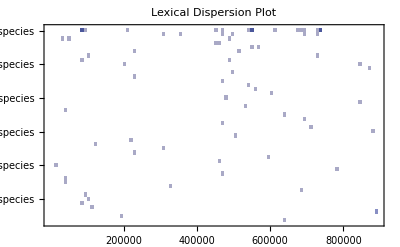

```mathematica
ols["LexicalDispersion"]
```

One may want to truncate the number of matches displayed, this can be done by setting the MaxItemspaclet:ref/MaxItems option.

Display the first 5 examples

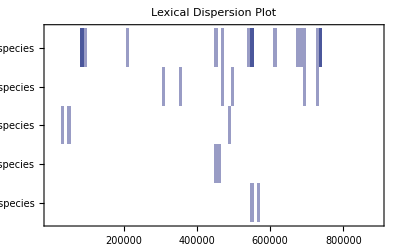

```mathematica
ols["LexicalDispersion",MaxItems->5]
```

As mentioned earlier, one can also use LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol. This function takes a string or list of strings as its first argument (the source) and a list of strings or lexical patterns as its second argument (the queries). In the case that multiples sources are given, multiple plots are returned. Set the DataJoin option to Truepaclet:ref/True to return a single plot.

Get a lexical dispersion plot of the 5 most common bigrams in the origin of species

```mathematica
bgrams=WordCounts[oosp,2][[;;5]]//Keys//Map[StringRiffle]
```

{of the,in the,the same,to the,on the}

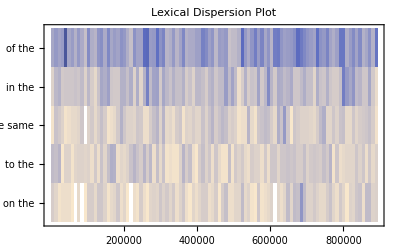

```mathematica
LexicalDispersionPlot[oosp,bgrams]
```

LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol also supports lexical patterns as the second argument.

Plot lexical dispersion as a MatrixPlotpaclet:ref/MatrixPlot

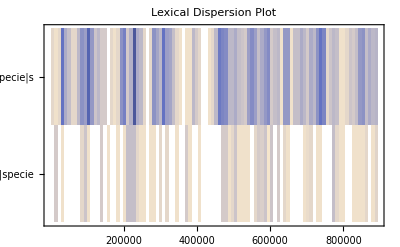

```mathematica
LexicalDispersionPlot[oosp,{
TextType["Adjective"]~~" "~~BoundToken["specie"|"species"],
TextType["Noun"]~~" "~~BoundToken["specie"|"species"]
}
]
```

Use LexicalDispersionSmoothHistogrampaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionSmoothHistogramFaizonZaman Package Symbol for the histogram variant of the same plot

Plot lexical dispersion as a SmoothHistogrampaclet:ref/SmoothHistogram

```mathematica
LexicalDispersionSmoothHistogram[oosp,{
TextType["Adjective"]~~" "~~BoundToken["specie"|"species"],
TextType["Noun"]~~" "~~BoundToken["specie"|"species"]
}
]
```

-Graphics-

For more information on LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol and LexicalDispersionSmoothHistogrampaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionSmoothHistogramFaizonZaman Package Symbol, see the documentation.

Searching Files and Services

### Services — Wikipedia

It's nice to be able to search strings, but one may want more data to search over. Using a "Content" or "Category" rule, or just a lexical pattern itself as input will search over Wikipedia. The MaxItemspaclet:ref/MaxItems option will restrict the number of articles collected. Note that when LexicalCases is given just a lexical pattern, and no source text, an attempt is made to convert the pattern to a Wikipedia search query, which might not always work.

Search over Wikipedia articles containing the keyword "science fiction"

```mathematica
scifi=LexicalCases["Content"->"science fiction",WordToken[1,"KeepContractions"]~~" car",MaxItems->1000];
```

```mathematica
scifi["CountGroups"]
```

### Files

LexicalCasespaclet:FaizonZaman/LexicalCases/ref/LexicalCasesFaizonZaman Package Symbol supports Filepaclet:ref/File objects, File paths and SearchIndexObjectpaclet:ref/SearchIndexObject's as input. If using a file-path string, surround it with either Filepaclet:ref/File or Listpaclet:ref/List. SearchIndexObjectpaclet:ref/SearchIndexObject's allow one to search over files in a particular set of directories. Use CreateSearchIndexpaclet:ref/CreateSearchIndex to make one. In LexicalCasespaclet:FaizonZaman/LexicalCases/ref/LexicalCasesFaizonZaman Package Symbol specify which files to use from the index by supplying a search query. This is done with a Rulepaclet:ref/Rule where the left-hand-side (lhs) is the index and the right-hand-side (rhs) is the search query.  A Stringpaclet:ref/String or SearchQueryStringpaclet:ref/SearchQueryString is valid rhs.

Built-in String Functions

If you prefer lightweight output, instead of the LexicalSummarypaclet:FaizonZaman/LexicalCases/ref/LexicalSummaryFaizonZaman Package Symbol object, consider using the LexicalPatternpaclet:FaizonZaman/LexicalCases/ref/LexicalPatternFaizonZaman Package Symbol wrapper with native String functions (Note: options are not supported at the moment).

Get example text

```mathematica
alice = ExampleData[{"Text","AliceInWonderland"}];
```

```mathematica
aliceVerbAdverbPattern=LexicalPattern["Alice "~~TextType["Verb"]~~TextType["Adverb"]];
```

Find cases of aliceVerbAdverbPattern in "Alice In Wonderland"

```mathematica
StringCases[alice, aliceVerbAdverbPattern]
```

{Alice had not,Alice was not,Alice went back,Alice took up,Alice had no,Alice was soon,Alice could only,Alice looked all,Alice could not,Alice was more,Alice crouched down,Alice went timidly,Alice was just,Alice looked down,Alice had not,Alice got up,Alice was very,Alice looked up,Alice was too,Alice got up}

Find string positions of aliceVerbAdverbPattern matches in "Alice In Wonderland"

```mathematica
StringPosition[alice, aliceVerbAdverbPattern]
```

{{1349,1361},{2548,2560},{4360,4374},{8488,8500},{16084,16095},{18290,18303},{22528,22543},{25145,25160},{26380,26394},{29462,29475},{30448,30466},{32290,32307},{35021,35034},{35170,35186},{36142,36154},{38307,38318},{43702,43715},{44556,44570},{44958,44970},{51619,51630}}

Check if a string matches aliceVerbAdverbPattern

```mathematica
StringMatchQ["Alice walked quickly", aliceVerbAdverbPattern]
```

True

Uppercase all verbs in a string

```mathematica
StringReplace["Alice walked quickly", LexicalPattern[v:TextType["Verb"]:>ToUpperCase[v]]]
```

Alice WALKED quickly

It's also possible to use the operator forms of these functions.

Define a Q operator for matching a lexical pattern

```mathematica
aliceVerbAdverbQ=StringMatchQ[aliceVerbAdverbPattern];
```

```mathematica
aliceVerbAdverbQ["Alice walked quickly"]
```

True

Abstractions

### LexicalMap

Map a function over lexical patterns in a string. This is effectively the same as using a LexicalPattern in StringReplace.

```mathematica
LexicalMap["**"<>#<>"**"&,"emphasize cool words",TextType["Adjective"]]
```

emphasize **cool** words

### LexigramCount

In NLP an n-gram is a length-n sequence of words (or perhaps lexemes). Similarly, the LexigramCountpaclet:FaizonZaman/LexicalCases/ref/LexigramCountFaizonZaman Package Symbol represents the 'length' of a lexical pattern.

Compute the LexigramCount for a lexical pattern

```mathematica
LexigramCount[TextType["Adjective"]~~" "~~BoundToken["specie"|"species"]]
```

3

The LexicalPattern here has 3 elements including the whitespace. Note below that OptionalTokenpaclet:FaizonZaman/LexicalCases/ref/OptionalTokenFaizonZaman Package Symbol is counted as the Interval 0 to the maximum LexigramCount of the optional token's arguments.

Compute the LexigramCount for a lexical pattern

```mathematica
patt=TextType["Adjective"]~~" "~~OptionalToken["green"]~~BoundToken["specie"|"species"];
LexicalCases["cool green species. amazing species",patt]
```

LexicalSummary[…]

```mathematica
LexigramCount[patt]
```

Interval[{3,4}]

Conclusion

LexicalCasespaclet:FaizonZaman/LexicalCases/ref/LexicalCasesFaizonZaman Package Symbol provides a set of lexical pattern objects, a way to query them on strings, files, and large datasets like Wikipedia articles, and easy access to properties of results. Additionally, one can use LexicalDispersionPlotpaclet:FaizonZaman/LexicalCases/ref/LexicalDispersionPlotFaizonZaman Package Symbol to see how these structures are used across a text. With this paclet, I hope lexical researchers and enthusiasts can easily explore lexical patterns in a consistent, wolfram language way. Feedback is welcome! Please send a message on the paclet repository, or visit the GitHubhttps://github.com/dishmint/LexicalCases repository.

| Related Guides
▪LexicalCasesOverview